# Homework 4

## Problem 4.1

The magnetic field of a wire is given by the expression B=0.305/r where r is in meters and B is in Tesla. The wire is on the z-axis and current flows in the +z direction. Recall that a right-hand rule will give you the direction of the field lines around the wire. A charge of +2.4 mC and mass 0.100 g moves under the influence of the magnetic field of the wire.   The initial conditions are: x(0)=0.100 m, y(0)=z(0)=0, vx(0)=vy(0)=0, vz(0)= 1.00 m/s. Plot the motion of the particle over the time interval 0 to 1 second.

```mathematica
Clear["`*"]
```

```mathematica
m=0.0001;
q=0.0024;
```

## Part A

Find the magnetic field as a function of x and y. (It is independent of z.) Be sure to put x[t] and y[t] in your equations, so that the t dependence of these variables will be evident when we put these in differential equations.

```mathematica
Bx=-0.305*y[t]/(x[t]^2+y[t]^2);
By=0.305*x[t]/(x[t]^2+y[t]^2);
```

### Hints

You can write the x - component of B as Bx = -B*y/r.Why?

### Solutions

```mathematica
Bx$=-.305*y[t]/(x[t]^2+y[t]^2);
By$=.305*x[t]/(x[t]^2+y[t]^2);
If[FullSimplify[Solve[Bx==Bx$,x[t]]]=={{}},Print["Bx is correct"],Print["Bx is incorrect"]];
If[FullSimplify[Solve[By==By$,y[t]]]=={{}},Print["By is correct"],Print["By is incorrect"]];
```

Bx is correct

By is correct

## Part B

Write down equations of motion for x, y, and z. You may write derivates either as x'' [ t ] or D[ x [ t ] , { t , 2 } ], etc.

```mathematica
eqx=m*x''[t]== q(y'[t]*0-z'[t]*By);
eqy=m*y''[t]== q(z'[t]*Bx-x'[t]*0);
eqz=m*z''[t]== q(x'[t]*By-y'[t]*Bx);
```

### Solutions

```mathematica
eqx$=m*D[x[t],{t,2}]==-q*z'[t]*By;
eqy$=m*y''[t]==q*z'[t]*Bx;
eqz$=m*z''[t]==q*(x'[t]*By-y'[t]*Bx);
ax1$=Dx2/.Solve[eqx$/.{x''[t]->Dx2},Dx2][[1]];
ax2$=Dx2/.Solve[eqx/.{x''[t]->Dx2},Dx2][[1]];
ay1$=Dy2/.Solve[eqy$/.{y''[t]->Dy2},Dy2][[1]];
ay2$=Dy2/.Solve[eqy/.{y''[t]->Dy2},Dy2][[1]];
az1$=Dz2/.Solve[eqz$/.{z''[t]->Dz2},Dz2][[1]];
az2$=Dz2/.Solve[eqz/.{z''[t]->Dz2},Dz2][[1]];
If[FullSimplify[Solve[(ax1$/.z'[t]->Dz)==(ax2$/.z'[t]->Dz),Dz]]=={{}},Print["eqx is correct."],Print["eqx is incorrect."]]
If[FullSimplify[Solve[(ay1$/.z'[t]->Dz)==(ay2$/.z'[t]->Dz),Dz]]=={{}},Print["eqy is correct."],Print["eqy is incorrect."]]
If[FullSimplify[Solve[(az1$/.x'[t]->Dx)==(az2$/.x'[t]->Dx),Dx]]=={{}},Print["eqz is correct."],Print["eqz is incorrect."]]
eqx$=m*D[x[t],{t,2}]==q*z'[t]*By;
eqy$=m*y''[t]==-q*z'[t]*Bx;
eqz$=m*z''[t]==-q*(x'[t]*By+y'[t]*Bx);
ax1$=Dx2/.Solve[eqx$/.{x''[t]->Dx2},Dx2][[1]];
ax2$=Dx2/.Solve[eqx/.{x''[t]->Dx2},Dx2][[1]];
ay1$=Dy2/.Solve[eqy$/.{y''[t]->Dy2},Dy2][[1]];
ay2$=Dy2/.Solve[eqy/.{y''[t]->Dy2},Dy2][[1]];
az1$=Dz2/.Solve[eqz$/.{z''[t]->Dz2},Dz2][[1]];
az2$=Dz2/.Solve[eqz/.{z''[t]->Dz2},Dz2][[1]];
If[FullSimplify[Solve[(ax1$/.z'[t]->Dz)==(ax2$/.z'[t]->Dz),Dz]]=={{}},Print["eqx has a minus sign error."]]
If[FullSimplify[Solve[(ay1$/.z'[t]->Dz)==(ay2$/.z'[t]->Dz),Dz]]=={{}},Print["eqy has a minus sign error."]]
If[FullSimplify[Solve[(az1$/.x'[t]->Dx)==(az2$/.x'[t]->Dx),Dx]]=={{}},Print["eqz has a minus sign error."]]
```

eqx is correct.

eqy is correct.

eqz is correct.

## Part C

(C) Solve these equations simultaneously.

I have left the first plot intact, so you can check your answer by comparing your plot to this plot.

0.0001 x''[t]==-(0.000732 x[t] z'[t])/(x[t]^2+y[t]^2)

0.0001 y''[t]==-(0.000732 y[t] z'[t])/(x[t]^2+y[t]^2)

0.0001 z''[t]==0.0024 ((0.305 x[t] x'[t])/(x[t]^2+y[t]^2)+(0.305 y[t] y'[t])/(x[t]^2+y[t]^2))

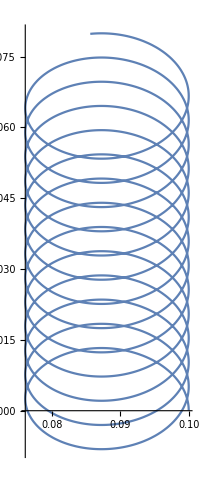

```mathematica
Print[eqx];
Print[eqy];
Print[eqz];
sol=NDSolve[{eqx,eqy,eqz,x[0]==0.1,y[0]==0,z[0]==0,x'[0]==0,y'[0]==0,z'[0]==1},{x,y,z},{t,0,1}];
ParametricPlot[Evaluate[{x[t],z[t]}/.sol],{t,0,1},PlotStyle->Automatic]
```

Be sure to rotate this plot so you can see the curve in three dimensions.

```mathematica
sol=NDSolve[{eqx,eqy,eqz,x[0]==0.1,y[0]==0,z[0]==0,x'[0]==0,y'[0]==0,z'[0]==1},{x,y,z},{t,0,1}];
```

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol],{t,0,1},PlotRange->{{0.05,0.1},{-0.05,0.05},{-0.1,0.1}},AxesLabel->{x,y,z}]
```

-Graphics3D-

## Part D

(D) Copy and paste the previous cells from Part C into the space below and play around with various initial conditions. You should see some interesting and nontrivial helical trajectories. You will probably have to adjust the plotting range to see the full trajectory.

```mathematica
sol=NDSolve[{eqx,eqy,eqz,x[0]==0.1,y[0]==0,z[0]==0,x'[0]==5,y'[0]==0.1,z'[0]==1},{x,y,z},{t,0,1}];
```

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol],{t,0,1},PlotRange->{{0.2,0.2},{-0.2,0.2},{-0.2,0.7}},AxesLabel->{x,y,z}]
```

-Graphics3D-

## Paper Problems